## 情報数学レポート 1SC16309Y田中雅也

## 3. 演習課題

### 問題 1. 第2節で行ったミニロトのシミュレーションを3番目の数だけでなく, 1, 2, 4, 5番目の数についても行う. 具体的には各x番目の数について, 100回のシミュレーションによる度数分布のグラフと 確率から計算された理論値の度数分布のグラフとを重ねて表示する.

```mathematica
Minilot:=Sort[RandomSample[Range[31],5]]
```

ミニロト100回のシミュレーションのリストをsim1とする.

```mathematica
sim1=Table[Minilot,{100}]
```

{{7,19,25,27,28},{7,13,18,25,26},{12,15,16,27,31},{2,3,9,21,29},{4,6,11,13,19},{7,9,16,21,24},{4,7,13,16,19},{4,7,13,15,29},{4,5,22,23,28},{4,11,21,23,31},{2,8,17,22,24},{10,11,23,25,26},{9,16,20,28,29},{18,20,24,25,29},{9,14,17,30,31},{9,13,27,28,30},{7,8,21,25,27},{3,5,17,26,29},{17,19,21,27,31},{3,6,18,24,27},{10,16,17,18,30},{7,8,14,21,25},{4,8,12,28,29},{9,11,21,27,28},{5,6,19,24,25},{4,10,19,22,30},{8,11,13,30,31},{8,18,19,29,30},{1,9,22,24,29},{8,10,23,29,30},{4,6,23,25,29},{4,8,15,21,29},{14,21,24,27,28},{3,13,14,26,31},{3,16,19,25,28},{1,3,5,6,23},{3,18,25,26,31},{7,20,21,24,25},{10,13,20,21,25},{3,4,18,26,31},{2,3,9,20,27},{7,11,12,17,31},{10,15,16,20,24},{5,10,18,29,31},{2,12,25,26,28},{15,16,17,20,23},{3,6,9,12,16},{2,3,5,19,24},{13,15,18,21,30},{4,8,11,15,30},{1,14,20,27,29},{8,9,16,19,20},{2,7,22,24,31},{4,7,9,18,30},{14,22,24,25,26},{5,6,7,8,11},{2,4,9,21,26},{3,14,18,20,27},{8,15,16,17,23},{9,14,22,24,28},{20,22,23,27,28},{2,7,11,15,17},{10,20,22,29,30},{9,14,24,28,31},{11,14,23,27,30},{4,6,22,29,31},{2,11,19,20,22},{3,6,7,11,27},{4,15,17,21,29},{1,3,4,13,29},{7,12,14,25,27},{4,5,11,20,21},{4,7,16,25,30},{3,10,24,29,31},{13,16,19,28,31},{1,7,12,25,27},{3,9,12,27,30},{3,6,15,16,19},{2,15,23,25,27},{4,5,17,21,29},{3,7,19,22,29},{3,7,15,17,21},{7,17,19,26,29},{2,3,4,16,21},{1,3,11,12,19},{2,7,10,25,26},{7,18,19,21,26},{2,11,20,28,29},{2,8,22,24,29},{3,5,8,13,28},{1,3,11,21,23},{8,10,13,21,25},{11,13,19,21,28},{8,16,20,27,29},{1,8,10,15,23},{1,12,15,20,23},{2,6,18,23,26},{8,12,19,29,30},{8,9,15,18,19},{2,9,13,24,26}}

リストsim1の各要素の1番目の数のリストをsim2とする.

```mathematica
sim2=Map[Function[x,x[[1]]],sim1]
```

{7,7,12,2,4,7,4,4,4,4,2,10,9,18,9,9,7,3,17,3,10,7,4,9,5,4,8,8,1,8,4,4,14,3,3,1,3,7,10,3,2,7,10,5,2,15,3,2,13,4,1,8,2,4,14,5,2,3,8,9,20,2,10,9,11,4,2,3,4,1,7,4,4,3,13,1,3,3,2,4,3,3,7,2,1,2,7,2,2,3,1,8,11,8,1,1,2,8,8,2}

リストsim2中の1から31までの出現回数のリストをsim3とする.

```mathematica
sim3=Table[Count[sim2,i],{i,1,31}]
```

{9,16,15,16,3,0,10,9,6,5,2,1,2,2,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0}

リストsim3を折れ線表示する.

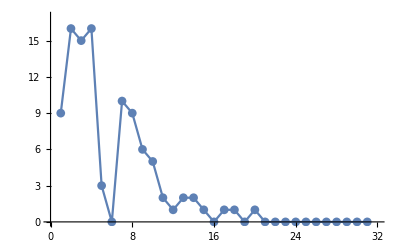

```mathematica
ListLinePlot[sim3,PlotRange->{{0,32},{0,Max[sim3]+1}},PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

1 から31の中からランダムに5個選び出した数字を小さい順番に並べ替えたリストを
{k,w,x,y,z} とする. 1番目の数字 k を固定すると
{w,x,y,z} は k+1から31の中から4個選ぶ場合の数 Binomial[31-k, 4] 通りある.
すなわち, 1番目の数がkとなるのは Binomial[31-k,4] 通りある.
1番目の数がkである確率を計算する関数 Loto1[k] を定義する.

```mathematica
Loto1[k_]:=Binomial[31-k,4]/Binomial[31,5]
```

100 回の試行での1番目の数字の度数の理論値は Loto1[k]*100 である.
この結果をリストminiloto3に代入しておく.

```mathematica
miniloto1=Table[N[Loto1[k]*100],{k,1,31}]
```

{16.129,13.9785,12.0504,10.3289,8.79872,7.44507,6.25386,5.21155,4.3052,3.52243,2.85149,2.28119,1.80094,1.40073,1.07115,0.803362,0.589132,0.420809,0.291329,0.194219,0.123594,0.0741565,0.041198,0.020599,0.00882815,0.00294272,0.000588543,0.,0.,0.,0.}

シミュレーション値と理論値を重ねて折れ線グラフを作成する.

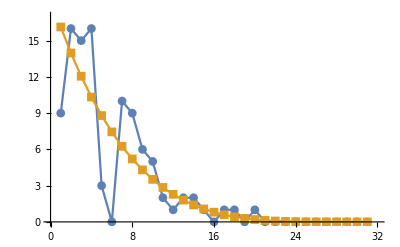

```mathematica
ListLinePlot[{sim3,miniloto1},PlotRange->{{0,32},{0,Max[sim3]+1}},PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

ミニロトの1番目の数の理論値の度数分布(miniloto1)で最大となる場所は

```mathematica
Position[miniloto1,Max[miniloto1]]
```

{{1}}

リストsim1の各要素の2番目の数のリストをsim4とする.

```mathematica
sim4=Map[Function[x,x[[2]]],sim1]
```

{19,13,15,3,6,9,7,7,5,11,8,11,16,20,14,13,8,5,19,6,16,8,8,11,6,10,11,18,9,10,6,8,21,13,16,3,18,20,13,4,3,11,15,10,12,16,6,3,15,8,14,9,7,7,22,6,4,14,15,14,22,7,20,14,14,6,11,6,15,3,12,5,7,10,16,7,9,6,15,5,7,7,17,3,3,7,18,11,8,5,3,10,13,16,8,12,6,12,9,9}

リストsim4中の1から31までの出現回数のリストをsim5とする.

```mathematica
sim5=Table[Count[sim4,i],{i,1,31}]
```

{0,0,8,2,5,10,10,8,6,5,7,4,5,6,6,6,1,3,2,3,1,2,0,0,0,0,0,0,0,0,0}

リストsim5を折れ線表示する.

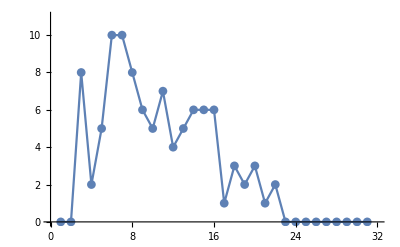

```mathematica
ListLinePlot[sim5,PlotRange->{{0,32},{0,Max[sim5]+1}},PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

1 から31の中からランダムに5個選び出した数字を小さい順番に並べ替えたリストを
{a,k,x,y,z} とする. 2番目の数字 k を固定すると
{a} は 1からk-1の中から1個選ぶ場合の数 Binomial[k-1, 1] 通りある.
{x,y,z} は k+1から31の中から3個選ぶ場合の数 Binomial[31-k, 3] 通りある.
すなわち, 2番目の数がkとなるのは Binomial[k-1,1]*Binomial[31-k,3] 通りある.
2番目の数がkである確率を計算する関数 Loto2[k] を定義する.

```mathematica
Loto2[k_]:=(Binomial[k-1,1]*Binomial[31-k,3])/Binomial[31,5]
```

100 回の試行での2番目の数字の度数の理論値は Loto2[k]*100 である.
この結果をリストminiloto2に代入しておく.

```mathematica
miniloto2=Table[N[Loto2[k]*100],{k,1,31}]
```

{0.,2.15054,3.85614,5.16447,6.12085,6.76825,7.14727,7.29617,7.25085,7.04486,6.70939,6.27328,5.76302,5.20272,4.61418,4.01681,3.42768,2.8615,2.33063,1.84508,1.4125,1.03819,0.725085,0.473777,0.282501,0.147136,0.0612085,0.0158907,0.,0.,0.}

シミュレーション値と理論値を重ねて折れ線グラフを作成する.

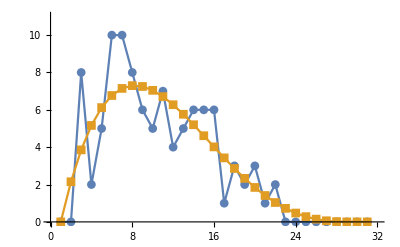

```mathematica
ListLinePlot[{sim5,miniloto2},PlotRange->{{0,32},{0,Max[sim5]+1}},PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

ミニロトの2番目の数の理論値の度数分布(miniloto1)で最大となる場所は

```mathematica
Position[miniloto2,Max[miniloto2]]
```

{{8}}

リストsim1の各要素の3番目の数のリストをsim6とする.

```mathematica
sim6=Map[Function[x,x[[3]]],sim1]
```

{25,18,16,9,11,16,13,13,22,21,17,23,20,24,17,27,21,17,21,18,17,14,12,21,19,19,13,19,22,23,23,15,24,14,19,5,25,21,20,18,9,12,16,18,25,17,9,5,18,11,20,16,22,9,24,7,9,18,16,22,23,11,22,24,23,22,19,7,17,4,14,11,16,24,19,12,12,15,23,17,19,15,19,4,11,10,19,20,22,8,11,13,19,20,10,15,18,19,15,13}

リストsim6中の1から31までの出現回数のリストをsim7とする.

```mathematica
sim7=Table[Count[sim6,i],{i,1,31}]
```

{0,0,0,2,2,0,2,1,5,2,6,4,5,3,5,6,7,7,11,5,5,7,6,5,3,0,1,0,0,0,0}

リストsim7を折れ線表示する.

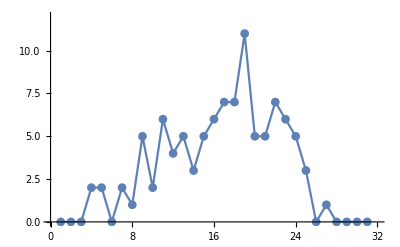

```mathematica
ListLinePlot[sim7,PlotRange->{{0,32},{0,Max[sim7]+1}},PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

1 から31の中からランダムに5個選び出した数字を小さい順番に並べ替えたリストを
{a,b,k,x,y} とする. 3番目の数字 k を固定すると
{a,b}は1からk-1の中から2個選ぶ場合の数Binomial[k-1,2]通りある.
{x,y} は k+1から31の中から2個選ぶ場合の数 Binomial[31-k, 2] 通りある.
すなわち, 3番目の数がkとなるのは Binomial[k-1,2]*Binomial[31-k,2] 通りある.
3番目の数がkである確率を計算する関数 Loto3[k] を定義する.

```mathematica
Loto3[k_]:=(Binomial[k-1,2]Binomial[31-k,2])/Binomial[31,5]
```

100 回の試行での3番目の数字の度数の理論値は Loto3[k]*100 である.
この結果をリストminiloto3に代入しておく.

```mathematica
miniloto3=Table[N[Loto3[k]*100],{k,1,31}]
```

{0.,0.,0.222469,0.619736,1.14766,1.76563,2.43657,3.12693,3.8067,4.44939,5.03205,5.53525,5.94311,6.24327,6.42689,6.48869,6.42689,6.24327,5.94311,5.53525,5.03205,4.44939,3.8067,3.12693,2.43657,1.76563,1.14766,0.619736,0.222469,0.,0.}

シミュレーション値と理論値を重ねて折れ線グラフを作成する.

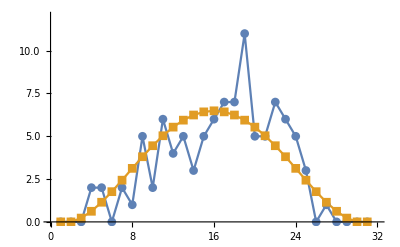

```mathematica
ListLinePlot[{sim7,miniloto3},PlotRange->{{0,32},{0,Max[sim7]+1}},PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

ミニロトの3番目の数の理論値の度数分布(miniloto3)で最大となる場所は

```mathematica
Position[miniloto3,Max[miniloto3]]
```

{{16}}

リストsim1の各要素の4番目の数のリストをsim8とする.

```mathematica
sim8=Map[Function[x,x[[4]]],sim1]
```

{27,25,27,21,13,21,16,15,23,23,22,25,28,25,30,28,25,26,27,24,18,21,28,27,24,22,30,29,24,29,25,21,27,26,25,6,26,24,21,26,20,17,20,29,26,20,12,19,21,15,27,19,24,18,25,8,21,20,17,24,27,15,29,28,27,29,20,11,21,13,25,20,25,29,28,25,27,16,25,21,22,17,26,16,12,25,21,28,24,13,21,21,21,27,15,20,23,29,18,24}

リストsim8中の1から31までの出現回数のリストをsim9とする.

```mathematica
sim9=Table[Count[sim8,i],{i,1,31}]
```

{0,0,0,0,0,1,0,1,0,0,1,2,3,0,4,3,3,3,2,7,13,3,3,8,12,6,10,6,7,2,0}

リストsim9を折れ線表示する.

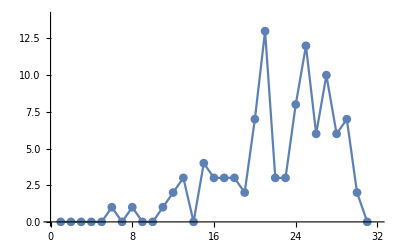

```mathematica
ListLinePlot[sim9,PlotRange->{{0,32},{0,Max[sim9]+1}},PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

1 から31の中からランダムに5個選び出した数字を小さい順番に並べ替えたリストを
{a,b,c,k,x} とする. 4番目の数字 k を固定すると
{a,b,c} は 1からk-1の中から3個選ぶ場合の数 Binomial[k-1, 3] 通りある.
{x} は k+1から31の中から1個選ぶ場合の数 Binomial[31-k, 1] 通りある.
すなわち, 4番目の数がkとなるのは Binomial[k-1,3]*Binomial[31-k,1] 通りある.
4番目の数がkである確率を計算する関数 Loto4[k] を定義する.

```mathematica
Loto4[k_]:=(Binomial[k-1,3]*Binomial[31-k,1])/Binomial[31,5]
```

100 回の試行での4番目の数字の度数の理論値は Loto4[k]*100 である.
この結果をリストminiloto4に代入しておく.

```mathematica
miniloto4=Table[N[Loto4[k]*100],{k,1,31}]
```

{0.,0.,0.,0.0158907,0.0612085,0.147136,0.282501,0.473777,0.725085,1.03819,1.4125,1.84508,2.33063,2.8615,3.42768,4.01681,4.61418,5.20272,5.76302,6.27328,6.70939,7.04486,7.25085,7.29617,7.14727,6.76825,6.12085,5.16447,3.85614,2.15054,0.}

シミュレーション値と理論値を重ねて折れ線グラフを作成する.

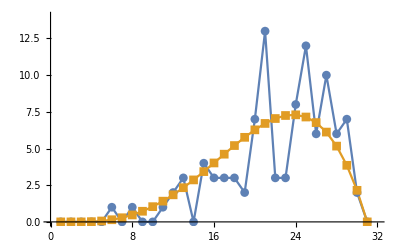

```mathematica
ListLinePlot[{sim9,miniloto4},PlotRange->{{0,32},{0,Max[sim9]+1}},PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

ミニロトの4番目の数の理論値の度数分布(miniloto4)で最大となる場所は

```mathematica
Position[miniloto4,Max[miniloto4]]
```

{{24}}

リストsim1の各要素の5番目の数のリストをsim10とする.

```mathematica
sim10=Map[Function[x,x[[5]]],sim1]
```

{28,26,31,29,19,24,19,29,28,31,24,26,29,29,31,30,27,29,31,27,30,25,29,28,25,30,31,30,29,30,29,29,28,31,28,23,31,25,25,31,27,31,24,31,28,23,16,24,30,30,29,20,31,30,26,11,26,27,23,28,28,17,30,31,30,31,22,27,29,29,27,21,30,31,31,27,30,19,27,29,29,21,29,21,19,26,26,29,29,28,23,25,28,29,23,23,26,30,19,26}

リストsim10中の1から31までの出現回数のリストをsim11とする.

```mathematica
sim11=Table[Count[sim10,i],{i,1,31}]
```

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,5,1,3,1,6,4,5,8,8,10,18,13,15}

リストsim11を折れ線表示する.

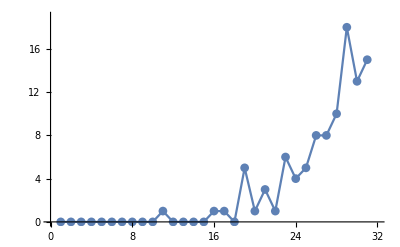

```mathematica
ListLinePlot[sim11,PlotRange->{{0,32},{0,Max[sim11]+1}},PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

1 から31の中からランダムに5個選び出した数字を小さい順番に並べ替えたリストを
{a,b,c,d,k} とする. 5番目の数字 k を固定すると
{a,b,c,d} は 1からk-1の中から4個選ぶ場合の数 Binomial[k-1, 4] 通りある.
すなわち, 5番目の数がkとなるのは Binomial[k-1,4] 通りある.
5番目の数がkである確率を計算する関数 Loto5[k] を定義する.

```mathematica
Loto5[k_]:=Binomial[k-1,4]/Binomial[31,5]
```

100 回の試行での5番目の数字の度数の理論値は Loto5[k]*100 である.
この結果をリストminiloto5に代入しておく.

```mathematica
miniloto5=Table[N[Loto5[k]*100],{k,1,31}]
```

{0.,0.,0.,0.,0.000588543,0.00294272,0.00882815,0.020599,0.041198,0.0741565,0.123594,0.194219,0.291329,0.420809,0.589132,0.803362,1.07115,1.40073,1.80094,2.28119,2.85149,3.52243,4.3052,5.21155,6.25386,7.44507,8.79872,10.3289,12.0504,13.9785,16.129}

シミュレーション値と理論値を重ねて折れ線グラフを作成する.

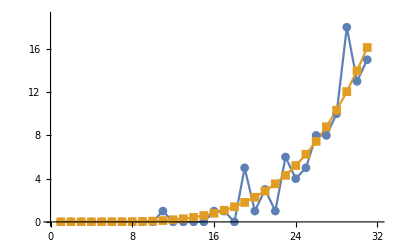

```mathematica
ListLinePlot[{sim11,miniloto5},PlotRange->{{0,32},{0,Max[sim11]+1}},PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

ミニロトの5番目の数の理論値の度数分布(miniloto5)で最大となる場所は

```mathematica
Position[miniloto5,Max[miniloto5]]
```

{{31}}

### 問題 2. 確率から計算された理論値の度数分布のグラフで 度数が最大となる場所の5つの数字を求めよ. すなわち, 5つの数字を {a, b, c, d, e} とするとき, a は 1から31から5つ選んで小さい順番に並べたときに1番目に来る数の中で 出現確率が一番大きな数である. 同様に, b,c,d,e についても考える. c は 3番目の来る数なので, 第2節の結果から c=16が最大確率である.

```mathematica
上記より{a,b,c,d,e}={1,8,16,24,31}
```

### 問題3. (問題2.)で選んだ5つの数字 {a, b, c, d, e} がミニロトで最も当たりやすいか?

```mathematica
当たりやすくはない！！
各項目ごとにこの数字が出やすいだけで、この５つの組み合わせになりやすいわけではない。
```